## 1. Naloga

1. podnaloga

```mathematica
v0={10,3};
GG=9.81;
H=10;
```

```mathematica
a={0, -GG};
x0={0, H};
```

```mathematica
v[t_]={v0[[1]], v0[[2]] - GG * t}
```

{10,3-9.81 t}

```mathematica
(*v[t_]:=v0+a*t*)
```

2. podnaloga

```mathematica
X[t_]:=x0+v0*t+a*t^2/2
```

```mathematica
X[t]
```

{10 t,10+3 t-4.905 t^2}

3. podnaloga

```mathematica
SlikaTocke[t_]:={PointSize[0.03],Point[X[t]]}
```

4. podnaloga

```mathematica
SlikaVektorja[t_]:={Arrow[t], Thickness[0.005]}
```

5. podnaloga

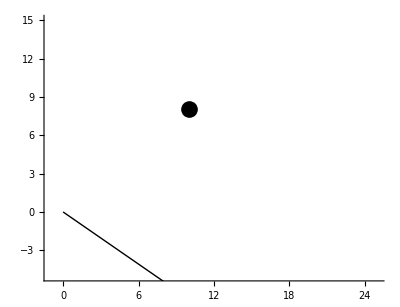

```mathematica
Graphics[{SlikaTocke[1],SlikaVektorja[{ {0,0},v[1]}]},Axes->True, PlotRange->{{-1,25},{-5,15}}, AspectRatio->Automatic]
```

6. podnaloga

```mathematica
Manipulate[Graphics[{SlikaTocke[t], SlikaVektorja[{ {0,0},v[t]}]},Axes->True, PlotRange->{{-1,25},{-5,15}}, AspectRatio->Automatic], {t, 0, 5}]
```

7. podnaloga

```mathematica
CasPadca=Solve[Last[X[t]] == 0 && t>0, t]
```

{{t→1.76604}}

8. podnaloga

```mathematica
Solve[Last[v[t]]==0]
```

{{t→0.30581}}

```mathematica
Last[X[0.3058103975535168]]
```

10.4587

9. podnaloga

```mathematica
Manipulate[Graphics[{SlikaTocke[t], SlikaVektorja[{ {0,0},v[t]}]},Axes->True, PlotRange->{{-1,18},{-2,12}},AspectRatio->Full], {t, 0, 5}]
```

10. podnaloga

```mathematica
Norm[v[1.7660350319649323]]
```

17.47

## 2. Naloga

```mathematica
r=Ravnina[{-1, -1, -1},{1,1,1}]
```

Ravnina[{-1,-1,-1},{1,1,1}]

1. podnaloga

```mathematica
Slika[Ravnina[n_,v_]]:=Hyperplane[n, v]
```

2. podnaloga

```mathematica
Format[r_Ravnina]:=Graphics3D[Slika[r]]
```

```mathematica
Format[r]
```

-Graphics3D-

3. podnaloga

```mathematica
Normala[Ravnina[n_,v_]]:=n
```

```mathematica
Tocka[Ravnina[n_,v_]]:=v
```

```mathematica
Normala[r]
Tocka[r]
```

{-1,-1,-1}

{1,1,1}

4. podnaloga

```mathematica
rx=Ravnina[{1, 0, 0},{0,0,0}]
ry=Ravnina[{0,1, 0},{0,0,0}]
rz=Ravnina[{0, 0, 1},{0,0,0}]
```

Ravnina[{1,0,0},{0,0,0}]

Ravnina[{0,1,0},{0,0,0}]

Ravnina[{0,0,1},{0,0,0}]

5. podnaloga

```mathematica
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v, v+n}]
```

```mathematica
Graphics3D[SlikaNormale[r]]
```

-Graphics3D-

6. podnaloga

```mathematica
Graphics3D[{Slika[r], Slika[rx], Slika[ry], Slika[rz],SlikaNormale[r], SlikaNormale[rx], SlikaNormale[ry], SlikaNormale[rz]}]
```

-Graphics3D-

7. podnaloga

```mathematica
Enacba[Ravnina[n_, v_]]:=Module[{a, b, c, d},
a = n[[1]];
b=n[[2]];
c=n[[3]];
d=Dot[n, v];
a*x+b*y+c*z-d==0
]
```

```mathematica
Enacba[r]
```

3-x-y-z==0

8. podnaloga

```mathematica
ResiSistem[sistem_List]:=Solve[{sistem[[1]], sistem[[2]], sistem[[3]]},{x,y,z}]
```

```mathematica
ResiSistem[{Enacba[r], Enacba[rx], Enacba[rz]}]
```

{{x→0,y→3,z→0}}

9. podnaloga

```mathematica
Presecisca[ravnine_]:=Map[Enacba, ravnine]//
Subsets[#, {3}]& //
Map[ResiSistem, #]&//
Map[First, #]&//
{{x,y,z} /. #)&
```

10. podnaloga

```mathematica
Vsebuje[Ravnina[n_,v_],x_,y_,z_,eps_:0.000001]:=Module[{tocka},
tocka = {x,y,z};
If[Dot[n, tocka]<eps, True];
If[Dot[n, tocka]>=eps, False];
]
```

## 3. Naloga

```mathematica
TezisceTrikotnika[a_, b_, c_]:=Module[{x1, x2, x3, y1, y2, y3, z1, z2, z3},
{x1, y1, z1} = a;
{x2, y2, z2}=b;
{x3, y3, z3}=c;
T={(x1+x2+x3)/3, (y1+y2+y3)/3, (z1 + z2 + z3)/3}
]
```

```mathematica
AA={3, 3, -1};
BB={2, 3, 1};
CC={1, 2, -1};
```

```mathematica
T=TezisceTrikotnika[AA, BB, CC];
```

```mathematica
AB=BB-AA;
AC=CC-AA;
```

```mathematica
n=-Cross[AB, AC]
```

{-2,4,-1}

```mathematica
Show[Graphics3D[{Arrow[{T, T+n}],Point[T],Line[{{1,2,-1},{2,3,1},{3,3,-1},{4,-3,1},{1,2,-1},{3,3,-1},{4,-3,1},{2,3,1}}]}],Axes->True]
```

-Graphics3D-